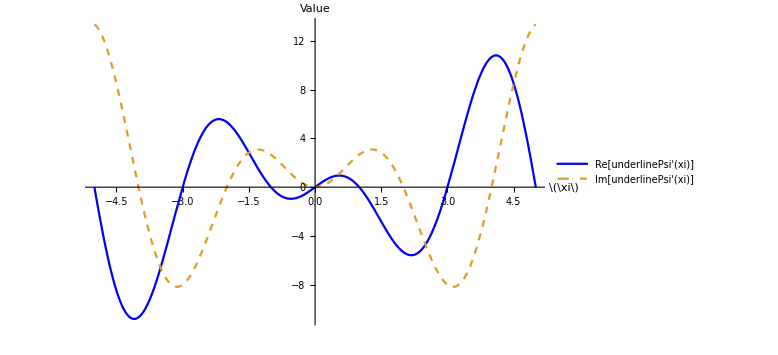

-Graphics-

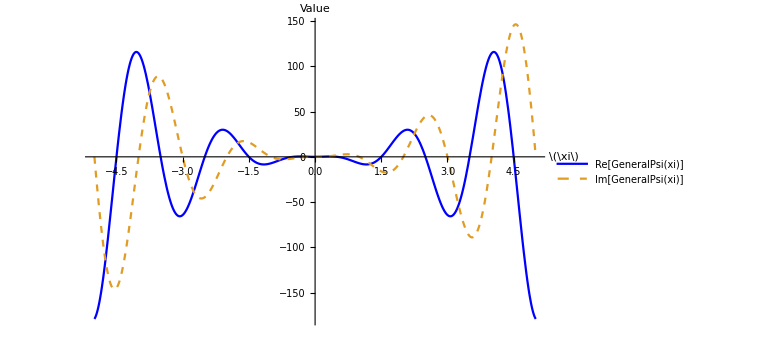

```mathematica
ClearAll["Global`*"];

(*Parameters for the first wavefunction*)
Z=I;(*Set to 1 (real) or I (complex)*)H=I;(*Set to 1 (real) or I (complex)*)Theta=1;(*Set to real or complex values*)Lambda=100;(*Lambda controls the curvature*)xiRange={-5,5};(*Range for xi values*)(*Define Xi_mu for one dimension*)Xi[xi_]:=xi;(*Xi is just the variable xi in this case*)(*Define the wavefunction underline psi'*)underlinePsiPrime[xi_]:=Lambda^2*((Z+H/(Lambda+Xi[xi]))^(Theta*(Lambda+Xi[xi]))-(-Z-H/(Lambda-Xi[xi]))^(Theta*(Lambda-Xi[xi])));

(*Plotting the first underline psi' wavefunction*)
underlinePsiPrimePlot=Plot[{Re[underlinePsiPrime[xi]],Im[underlinePsiPrime[xi]]},{xi,xiRange[[1]],xiRange[[2]]},PlotStyle->{{Blue,Thick},{Gold,Dashed}},PlotRange->All,AxesLabel->{"\(\xi\)","Value"},PlotLegends->{"Re[underlinePsi'(xi)]","Im[underlinePsi'(xi)]"},ImageSize->Large];
underlinePsiPrimePlot

(*Parameters for the second wavefunction*)
Z2=I;(*Set to 1 (real) or I (complex)*)H2=I;(*Set to 1 (real) or I (complex)*)Theta2=1;(*Set to real or complex values*)Lambda2=100;(*Lambda controls the curvature*)xiRange2={-5,5};(*Range for xi values*)(*Define Xi_mu for the second wavefunction*)Xi2[xi_]:=xi;

(*Define the second underline psi' wavefunction*)
underlinePsiPrime2[xi_]:=Lambda2^2*((Z2+H2/(Lambda2+Xi2[xi]))^(Theta2*(Lambda2+Xi2[xi]))-(-Z2-H2/(Lambda2-Xi2[xi]))^(Theta2*(Lambda2-Xi2[xi])));

(*Plotting the second underline psi' wavefunction*)
underlinePsiPrime2Plot=Plot[{Re[underlinePsiPrime2[xi]],Im[underlinePsiPrime2[xi]]},{xi,xiRange2[[1]],xiRange2[[2]]},PlotStyle->{{Blue,Thick},{Gold,Dashed}},PlotRange->All,AxesLabel->{"\(\xi\)","Value"},PlotLegends->{"Re[underlinePsi'(xi)]","Im[underlinePsi'(xi)]"},ImageSize->Large];
underlinePsiPrime2Plot

(*General wavefunction combination logic*)
a1=1;(*Power for the first Psi'*)a2=1;(*Power for the second Psi'*)b1=1;(*Power for the first underline Psi'*)b2=1;(*Power for the second underline Psi'*)(*Define the generalized equation combining all wavefunctions*)generalPsi[xi_]:=((underlinePsiPrime[xi]^a1)*(underlinePsiPrime2[xi]^a2));

(*Plot the general wavefunction*)
generalPsiPlot=Plot[{Re[generalPsi[xi]],Im[generalPsi[xi]]},{xi,xiRange2[[1]],xiRange2[[2]]},PlotStyle->{{Blue,Thick},{Gold,Dashed}},PlotRange->All,AxesLabel->{"\(\xi\)","Value"},PlotLegends->{"Re[GeneralPsi(xi)]","Im[GeneralPsi(xi)]"},ImageSize->Large];
generalPsiPlot
```